```mathematica
X0={x0,y0,z0};
X={x,y,z};
v={vx,vy.vz};
A={ax,ay,az};
B={bx,by,bz};
R={a,b,c};
Len[X_]:=Sqrt[Dot[X,X]];

sol=Solve[{D[Len[Cross[X0-B,X0-A]]/Len[B-A],{X0}]==0,Dot[X0/(R R),B-A]==0},X0][[1]]
```

{x0→(a^2 (az^2 b^2 bx-ax az b^2 bz-az b^2 bx bz+ax b^2 bz^2+ay^2 bx c^2-ax ay by c^2-ay bx by c^2+ax by^2 c^2))/(a^2 az^2 b^2-2 a^2 az b^2 bz+a^2 b^2 bz^2+a^2 ay^2 c^2+ax^2 b^2 c^2-2 ax b^2 bx c^2+b^2 bx^2 c^2-2 a^2 ay by c^2+a^2 by^2 c^2),y0→-((-a^2 az^2 b^2 by+a^2 ay az b^2 bz+a^2 az b^2 by bz-a^2 ay b^2 bz^2+ax ay b^2 bx c^2-ay b^2 bx^2 c^2-ax^2 b^2 by c^2+ax b^2 bx by c^2)/(a^2 az^2 b^2-2 a^2 az b^2 bz+a^2 b^2 bz^2+a^2 ay^2 c^2+ax^2 b^2 c^2-2 ax b^2 bx c^2+b^2 bx^2 c^2-2 a^2 ay by c^2+a^2 by^2 c^2)),z0→-((ax az b^2 bx c^2-az b^2 bx^2 c^2+a^2 ay az by c^2-a^2 az by^2 c^2-a^2 ay^2 bz c^2-ax^2 b^2 bz c^2+ax b^2 bx bz c^2+a^2 ay by bz c^2)/(a^2 az^2 b^2-2 a^2 az b^2 bz+a^2 b^2 bz^2+a^2 ay^2 c^2+ax^2 b^2 c^2-2 ax b^2 bx c^2+b^2 bx^2 c^2-2 a^2 ay by c^2+a^2 by^2 c^2))}

```mathematica
(*kontrola: X0 leží na přímce*)
Solve[(A-X0/.sol)==k(A-B),k]  ;
```

```mathematica
sol2=Solve[Dot[(X0-t X0/(R R))/R,(X0-t X0/(R R))/R]-1==0/.sol,t][[2]];
```

```mathematica
P=X0/.sol2;
d2[ax_,ay_,az_,bx_,by_,bz_,a_,b_,c_]=Module[{ro=P/R,rd=-Normalize[P/(R R R)]},v=ro;dt= Dot[rd,v];sqt=√(dt^2-Dot[v,v]+1);Sign[-dt-sqt]*Len[(dt+sqt)R rd]]/.sol;
```

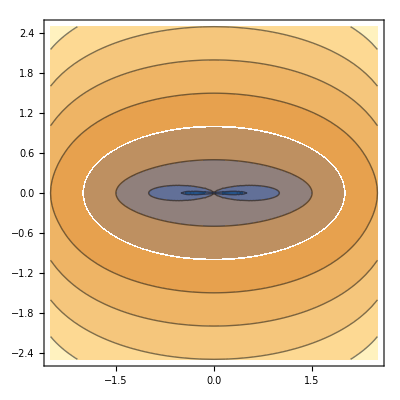

```mathematica
ContourPlot[d2[x,y,-1,x,y,0,2,1,1],{x,-2.5,2.5},{y,-2.5,2.5}]
```